```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/y/Nutstore Files/1Project/1QSTdisentanglement/7MLST/6Reply4/Nq3/shot_v3_Nq3shot100

```mathematica
lossqID2= Import["loss_Nj3.txt","Data"];
lossqID1= Import["loss_Nj2.txt","Data"];
lossqID0= Import["loss_Nj1.txt","Data"];
lossqID0⟦All,1⟧=lossqID0⟦All,1⟧+1;
lossqID1⟦All,1⟧=lossqID1⟦All,1⟧+1;
lossqID2⟦All,1⟧=lossqID2⟦All,1⟧+1;
lossqID0⟦All,2⟧=(lossqID0⟦All,2⟧+1)/2;
lossqID1⟦All,2⟧=(lossqID1⟦All,2⟧+1)/2;
lossqID2⟦All,2⟧=(lossqID2⟦All,2⟧+1)/2;
lossqID0⟦All,3⟧=(lossqID0⟦All,3⟧+1)/2;
lossqID1⟦All,3⟧=(lossqID1⟦All,3⟧+1)/2;
lossqID2⟦All,3⟧=(lossqID2⟦All,3⟧+1)/2;
loss = Join[{lossqID0⟦All,{1,2}⟧},{lossqID1⟦All,{1,2}⟧},{lossqID2⟦All,{1,2}⟧}];
lossEx = Join[{lossqID0⟦All,{1,3}⟧},{lossqID1⟦All,{1,3}⟧},{lossqID2⟦All,{1,3}⟧}];
Purity = Join[{lossqID0⟦All,{1,4}⟧},{lossqID1⟦All,{1,4}⟧},{lossqID2⟦All,{1,4}⟧}];
```

```mathematica
Figloss=ListLinePlot[loss,PlotRange->{{0,300},{-0.05,0.9}},PlotStyle->Dashed,GridLines->{{},{0.}},
FrameLabel->{Style["Epoch",Black,Directive[Large],FontSize->20],Style["ℒ",Italic,Directive[Large],Black,FontSize->20]},RotateLabel->False,

Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[Black,Bold,16],PlotMarkers->{"○", "□", "◇"},
FrameTicks->{{{0,0.2,0.4,0.6,0.8,{1.0,"1.0"}},None},{{0,100,200,300,400,600,750,900},None}},
PlotLegends->Placed[{Style["qubit=1",Bold,FontSize->14],Style["qubit=2",Bold,FontSize->14],Style["qubit=3",Bold,FontSize->14],Style["qubit=4",Bold,FontSize->14]},{0.78,0.44}],
ImageSize->{600,400},ImagePadding->{{80,80},{60,60}}]
```

-Graphics-

```mathematica
FiglossEx=ListLinePlot[lossEx,PlotRange->{{0,300},{-0.05,1.1}},
FrameLabel->{Style["Epoch",Black,Directive[Large],FontSize->20],Style["ℒ",Italic,Directive[Large],Black,FontSize->20]},RotateLabel->False,

Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[Black,Bold,16],PlotMarkers->{"•", "▪", {"◆",Offset[5]}},
FrameTicks->{{{0,0.2,0.4,0.6,0.8,{1.0,"1.0"}},None},{{0,150,300,450,600,750,900},None}},
ImageSize->{600,400},ImagePadding->{{80,80},{60,60}}]
```

-Graphics-

```mathematica
Figloss=Show[Figloss,FiglossEx]
```

-Graphics-

```mathematica
Export["shot100.pdf",Fig]
```

shot100.pdf

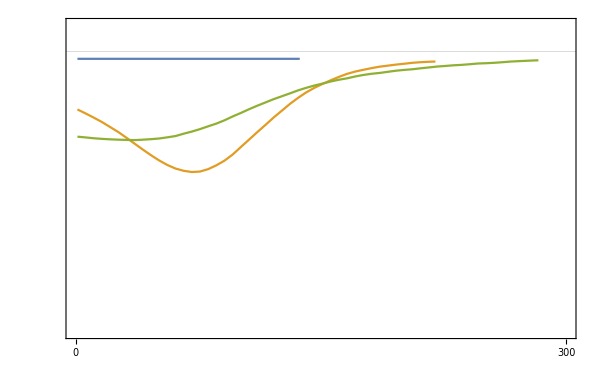

```mathematica
FigPurity=ListLinePlot[Purity,PlotRange->{{0,300},{-0.05,1.1}},GridLines->{{},{1.0}},
FrameLabel->{{None,Style["𝒫",Black,Italic,Directive[Large],FontSize->22]},{None,Style["shots = 100",FontSize->22]}},RotateLabel->False,
Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[Black,Bold,16],FrameTicks->{{None,{0,0.2,0.4,0.6,0.8,{1.0,"1.0"}}},{{0,300},None}},
ImageSize->{600,400},ImagePadding->{{80,80},{60,60}}]
```

```mathematica
Fig=Overlay[{FigPurity,Figloss}]
```

-Graphics--Graphics-

```mathematica
Export["Figshot100.jpeg",Fig,"jpeg"]
```

Figshot100.jpeg